Acoustic Power Transmission Coefficient Equation (SI)

```mathematica
T[v_, S_,f_,Lprime_,Sb_,h_,r_]:=((1+(((v/(2*S))/(((f*(2*Pi))*Lprime/Sb)-(v^2/((f*(2*Pi))*Pi*(r^2)*h)))))^2)^-1)(*Power transmission Equation (Angular freq units conversion)*)
L[f_,Lprime_,Sb_,h_,r_]:=T[590.5,0.03810,f,Lprime,Sb,h,r] (*Power transmission with the values for our engine substituted*)
J[Lprime_?NumericQ,Sb_?NumericQ,h_?NumericQ,r_?NumericQ]:=NIntegrate[L[f,Lprime, Sb, h, r],{f,350,383.333}](*Integration of the power transmission coeffiecient over the relevant range*)
B[Lprime_,Sb_, h_,r_] := (590.5/(2*Pi))* Sqrt[Sb/(Lprime*Pi*(r^2)*h)](*Formula to determine resonance frequency for given variables*)
NMinimize[{J[Lprime, Sb, h,r], 0.0254<Lprime-(1.7*Sqrt[Sb/Pi])<0.102,0.00050670737368<Sb<0.0011399977,0.0127<r<0.0635, 0.0127<h<0.1524,Lprime-(1.7*Sqrt[Sb/Pi])> (r-Sqrt[Sb/Pi]) + ((Sb*1550)/(4*39.37)),B[Lprime,Sb,h,r]==366.66667}, {Lprime, Sb,h,r}, MaxIterations->500](*Minimize transmission frequency in the given range of dimensions*)
(*Length 1 to 4 in (plus 0.85 * radius end correction), diameter tube 0.5 in to 1.5 in, cavity max length 6 inches, max diameter 5 in, L>(R-r)+Pi(r^2)/4 constraint on neck length (last section in inches)*)
```

{14.6324,{Lprime→0.0772972,Sb→0.00106701,h→0.0993808,r→0.0538946}}

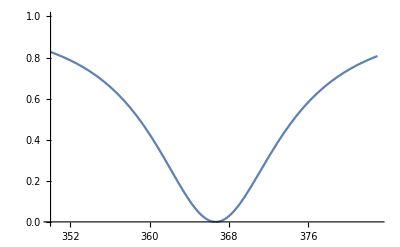

```mathematica
T[v_, S_,f_,Lprime_,Sb_,h_,r_]:=((1+(((v/(2*S))/(((f*(2*Pi))*Lprime/Sb)-(v^2/((f*(2*Pi))*Pi*(r^2)*h)))))^2)^-1)(*Power transmission Equation (Angular freq units conversion)*)
L[f_,Lprime_,Sb_,h_,r_]:=T[590.5,0.03810,f,Lprime,Sb,h,r] (*Power transmission with the values for our engine substituted*)
Plot[L[f,0.10376744155780149,0.001313439083,0.13036126539884924,0.0450596], {f,350,383}, PlotRange->{0,1}]
(*Current Setup*)
```

Second try to optimize by minimizing quality factor (MUCH FASTER and pseudo convergent to previous method!)

```mathematica
B[Lprime_,Sb_, h_,r_] := (590.5/(2*Pi))* Sqrt[Sb/(Lprime*Pi*(r^2)*h)](*Formula to determine resonance frequency for given variables*)
Q[Lprime_,Sb_,h_,r_]:=2*Pi*Sqrt[Pi*(r^2)*h*((Lprime/Sb)^3)]
NMinimize[{Q[Lprime, Sb, h,r], 0.0254<Lprime-(1.7*Sqrt[Sb/Pi])<0.102,0.00050670737368<Sb<0.0011399977,0.0127<r<0.0635, 0.0127<h<0.1524,Lprime-(1.7*Sqrt[Sb/Pi])> (r-Sqrt[Sb/Pi]) + ((Sb*1550)/(4*39.37)),B[Lprime,Sb,h,r]==366.666667}, {Lprime, Sb,h,r}, MaxIterations->500](*Minimize transmission frequency in the given range of dimensions*)
```

{100.824,{Lprime→0.0713708,Sb→0.00114,h→0.1524,r→0.0468159}}

13.8111

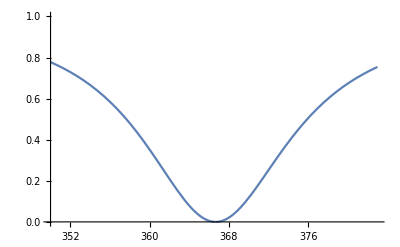

```mathematica
T[v_, S_,f_,Lprime_,Sb_,h_,r_]:=((1+(((v/(2*S))/(((f*(2*Pi))*Lprime/Sb)-(v^2/((f*(2*Pi))*Pi*(r^2)*h)))))^2)^-1)(*Power transmission Equation (Angular freq units conversion)*)
L[f_,Lprime_,Sb_,h_,r_]:=T[590.5,0.03810,f,Lprime,Sb,h,r] (*Power transmission with the values for our engine substituted*)
J[Lprime_?NumericQ,Sb_?NumericQ,h_?NumericQ,r_?NumericQ]:=NIntegrate[L[f,Lprime, Sb, h, r],{f,350,383.333}](*Integration of the power transmission coeffiecient over the relevant range*)
J[0.08876151648447288,0.0013134,0.15239999995042156,0.0450596]
Plot[L[f,0.08876151648447288,0.0013134,0.15239999995042156,0.0450596], {f,350,383}, PlotRange->{0,1}]
```

FINAL With pipe size constraints, and streamlining for both types:

0.0450596

19.0717

{0.0781008,0.000729541,0.096207}

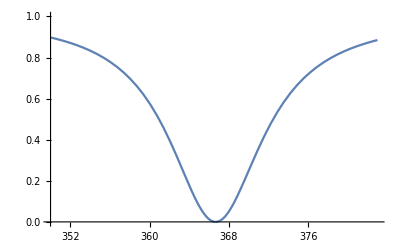

13.8111

{0.0766023,0.00113348,0.1524}

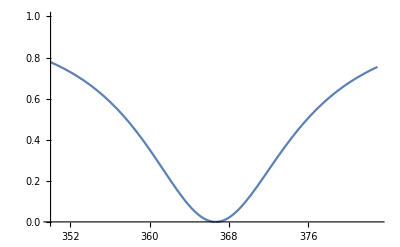

```mathematica
T[v_, S_,f_,Lprime_,Sb_,h_,r_]:=((1+(((v/(2*S))/(((f*(2*Pi))*Lprime/Sb)-(v^2/((f*(2*Pi))*Pi*(r^2)*h)))))^2)^-1)(*Power transmission Equation (Angular freq units conversion)*)
L[f_,Lprime_,Sb_,h_,r_]:=T[590.5,0.03810,f,Lprime,Sb,h,r] (*Power transmission with the values for our engine substituted*)
J[Lprime_?NumericQ,Sb_?NumericQ,h_?NumericQ,r_?NumericQ]:=NIntegrate[L[f,Lprime, Sb, h, r],{f,350,383.333}](*Integration of the power transmission coeffiecient over the relevant range*)
B[Lprime_,Sb_, h_,r_] := (590.5/(2*Pi))* Sqrt[Sb/(Lprime*Pi*(r^2)*h)](*Formula to determine resonance frequency for given variables*)
r=0.0450596
output={Lprime,Sb,h}/.NMinimize[{J[Lprime, Sb, h,r], 0.0254<Lprime-(1.7*Sqrt[Sb/Pi])<0.102,0.00050670737368<Sb<0.001313436083,0.0127<h<0.1524,Lprime-(1.7*Sqrt[Sb/Pi])> (r-Sqrt[Sb/Pi]) + ((Sb*1550)/(4*39.37)),B[Lprime,Sb,h,r]==366.667}, {Lprime,Sb, h}, MaxIterations->500,Method->{"RandomSearch","SearchPoints"->250}][[2]];(*Minimize transmission frequency in the given range of dimensions (IN SCHEDULE INCREMENTS)*)
J[output[[1]],output[[2]],output[[3]],r] (*Integral of power transmission coeff*)
Print[output]
Plot[L[f,output[[1]],output[[2]],output[[3]],r], {f,350,383}, PlotRange->{0,1}]
Q[Lprime_,Sb_,h_,r_]:=2*Pi*Sqrt[Pi*(r^2)*h*((Lprime/Sb)^3)]
output={Lprime,Sb,h}/.NMinimize[{Q[Lprime, Sb, h,r], 0.0254<Lprime-(1.7*Sqrt[Sb/Pi])<0.102,0.00050670737368<Sb<0.001313436083,0.0127<h<0.1524,Lprime-(1.7*Sqrt[Sb/Pi])> (r-Sqrt[Sb/Pi]) + ((Sb*1550)/(4*39.37)),B[Lprime,Sb,h,r]==366.667}, {Lprime,Sb, h}, MaxIterations->500,Method->{"RandomSearch","SearchPoints"->250}][[2]];(*Minimize transmission frequency in the given range of dimensions*)
J[output[[1]],output[[2]],output[[3]],r](*Integral of power transmission coeff*)
Print[output]
Plot[L[f,output[[1]],output[[2]],output[[3]],r], {f,350,383}, PlotRange->{0,1}]
```